```mathematica
Integrate[Exp[-1/2(Subscript[λ, 1]^2+Subscript[λ, 2]^2+Subscript[λ, 3]^2+Subscript[λ, 4]^2)] Det[VandermondeMatrix[{Subscript[λ, 1],Subscript[λ, 2],Subscript[λ, 3],Subscript[λ, 4]}]]^2,{Subscript[λ, 1],-∞,∞},{Subscript[λ, 2],-∞,∞},{Subscript[λ, 3],-∞,∞},{Subscript[λ, 4],-∞,∞}]
```

```mathematica
1152 π^2
```

```mathematica
Integrate[Exp[-1/2(Subscript[λ, 1]^2+Subscript[λ, 2]^2+Subscript[λ, 3]^2)] Det[VandermondeMatrix[{Subscript[λ, 1],Subscript[λ, 2],Subscript[λ, 3]}]]^2,{Subscript[λ, 1],-∞,∞},{Subscript[λ, 2],-∞,∞},{Subscript[λ, 3],-∞,∞}]
```

24 √2 π^(3/2)

```mathematica
1/(1152 π^2)Integrate[Exp[-1/2(Subscript[λ, 1]^2+Subscript[λ, 2]^2+Subscript[λ, 3]^2)] Det[VandermondeMatrix[{Subscript[λ, 1],Subscript[λ, 2],Subscript[λ, 3],λ}]]^2,{Subscript[λ, 1],-∞,∞},{Subscript[λ, 2],-∞,∞},{Subscript[λ, 3],-∞,∞}]
```

(9+9 λ^2-3 λ^4+λ^6)/(24 √(2 π))

```mathematica
ρ[n_, λ_]:=1/(4 √(2π)) Exp[-1/2 λ^2] Sum[HermiteH[j, λ/(√2)] HermiteH[j, λ/(√2)]/(2^j Factorial[j]),{j,0,n-1}]//ExpandAll;
```

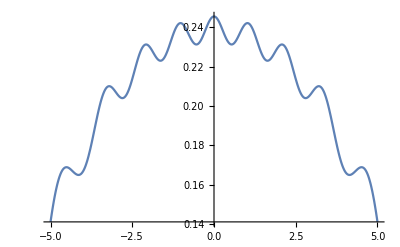

```mathematica
Plot[ρ[9, λ], {λ, -5, 5}]
```

```mathematica
%439==%440//FullSimplify
```

True

```mathematica
(4 √2 (9+9 λ^2-3 λ^4+λ^6))/(9+9 λ^2-3 λ^4+λ^6)
```

4 √2

```mathematica
1/(24 √2 π^(3/2))Integrate[Exp[-1/2(Subscript[λ, 1]^2+Subscript[λ, 2]^2+Subscript[λ, 3]^2+Subscript[λ, 4]^2)] Det[VandermondeMatrix[{Subscript[λ, 1],Subscript[λ, 2],Subscript[λ, 3],Subscript[λ, 4]}]]^2,{Subscript[λ, 1],-∞,∞},{Subscript[λ, 2],-∞,∞},{Subscript[λ, 3],-∞,∞}]
```

```mathematica
NRoots[(9+9 λ^2-3 λ^4+λ^6)==0,λ]
```

λ==-1.63135-0.884128 ⅈ||λ==-1.63135+0.884128 ⅈ||λ==0.-0.871338 ⅈ||λ==0.+0.871338 ⅈ||λ==1.63135-0.884128 ⅈ||λ==1.63135+0.884128 ⅈ

```mathematica
VandermondeMatrix
```

```mathematica
{Subscript[λ, 1]+Subscript[λ, 2]+Subscript[λ, 3]}
```

{λ_1+λ_2+λ_3}

```mathematica
Product
```

```mathematica
Times @@ (Table[(Subscript[λ, i]-Subscript[λ, j]),{i,1,3},{j,1,i-1}]//Flatten)
```

(-λ_1+λ_2) (-λ_1+λ_3) (-λ_2+λ_3)

```mathematica
Det[VandermondeMatrix[{Subscript[λ, 1],Subscript[λ, 2],Subscript[λ, 3]}]]^2
```

(-λ_1+λ_2)^2 (-λ_1+λ_3)^2 (-λ_2+λ_3)^2